## Load Data

```mathematica
ClearAll["Global`*"]
mydata=Import[StringJoin[NotebookDirectory[],"data/ExampleFreezeOut.mx"]];
Keys[mydata]

dαs=mydata["Alpha"][[2;;]]-mydata["Alpha"][[1;;-2]];
αs=mydata["Alpha"];
urs=Sinh[ArcTanh[(Transpose@mydata["BackgroundFields"])[[1]]]]; (*dimensionless*)
uτs=Cosh[ArcTanh[(Transpose@mydata["BackgroundFields"])[[1]]]]; (*dimensionless*)
rs=mydata["Radius"];(*in IGeV*)
Drs=mydata["RadialDerivative"];(*in IGeV*)
τs=mydata["Time"];(*in IGeV*)
Dτs=mydata["TimeDerivative"];(*in IGeV*)
```

{BackgroundFields,Alpha,Time,Radius,NumberOfPoints,TimeDerivative,RadialDerivative,MidpointRule,rStart,tStart,CentralityClass}

```mathematica
headers={"alpha","tau","r","Dtau","Dr","ur","utau"};
data=Transpose@{
αs,(*dimensionless*)
τs,(*in fm/c*)
rs,(*in fm*)
Dτs,(*in fm/c*)
Drs,(*in fm*)
urs,
uτs
};
exportdata=Prepend[data,headers];
Export[StringJoin[NotebookDirectory[],"data/ExampleFreezeOut.csv"],exportdata,"CSV"];
Export[StringJoin[NotebookDirectory[],"data/ExampleFreezeOut.txt"],{
{1,2,3},{10,20,30}},
"List"];
(*FreezeOutPlot=ListPlot[Transpose[{mydata["Radius"],mydata["Time"]}],AxesLabel->{r,τ}]*)
```

The αs are not at all evenly spaced and their spacing varies quite discontinuously.

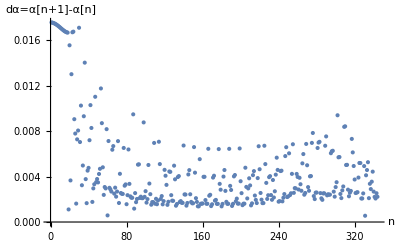

```mathematica
(*ListPlot[Transpose@{αs[[1;;-2]],dαs},AxesLabel->{"α","dα"}]*)
ListPlot[dαs,AxesLabel->{"n","dα=α[n+1]-α[n]"}]
```

### Define Interpolating Functions from the Data

NOTATION: an object named "fs" (where "f" stands for any of τ,α,ur,...) refers to an array of values of the corresponding quantity evaluated on the freezeout surface, as a function of α. So Transpose{αs,fs} are the (x,y)-value pairs corresponding to the function f[α]. Here we reconstruct the corresponding functions from interpolation, assuming they are sufficiently smooth and well resolved. The necessity of interpolated functions on the FO surface becomes clear later on.

```mathematica
ur=Interpolation[Transpose@{αs,urs}];
uτ=Interpolation[Transpose@{αs,uτs}];
r=Interpolation[Transpose@{αs,rs}];
Dr=Interpolation[Transpose@{αs,Drs}];
τ=Interpolation[Transpose@{αs,τs}];
Dτ=Interpolation[Transpose@{αs,Dτs}];
```

## Compute Field on Freezeout Surface

```mathematica
GeVtoIfm=5.0677;(*5.0677;(*1GeV=5.0677(fm^-1)\[hbar]c*)*)
IfmtoGeV=1/GeVtoIfm;
fmtoIGeV=GeVtoIfm;
IGeVtofm=1/fmtoIGeV;
mσ=0.6;(*mass of the sigma field ~ 400-800 MeV in GeV*)
ϵ=0.01*0.160054;(*energy density at freeze out in GeV/(fm^3)*)
vev=0.15;(*??? vev of sigma field ??? pion decay constant ???, in GeV*)
χ2=(-mσ^2+2*mσ*Sqrt[3*ϵ*(IfmtoGeV^3)/vev^2+mσ^2])/6;(*in GeV^2*)
χ=Sqrt[χ2];(*in GeV*)
(*θ0=0.5; This will be taken care of later*)

(*θ[α_?NumericQ]:=χ*NIntegrate[(Dτ[αprime]uτ[αprime]-Dr[αprime]*ur[αprime])*fmtoIGeV,{αprime,0,α}];*)
ρ=Sqrt[vev*(2*χ2+mσ^2)/(mσ^2)];(*in GeV*)
(*ϕfreezes:=ρ*Exp[I*θs];(*in GeV*)
π0s:=Sqrt[2]*Im[ϕfreezes];(*in GeV*)
σ0s:=Sqrt[2]*Re[ϕfreezes];(*in GeV*)*)
```

Evaluating θ via numerical integration seems to be very slow. This is a problem: Later a call to NIntegrate[(some function of θ[α]),{α, ... , ... }] is necessary (discussion later), but nested calls to NIntegrate a slow and "nesty" :)

```mathematica
θ[α_?NumericQ]:=χ*NIntegrate[(Dτ[αprime]uτ[αprime]-Dr[αprime]*ur[αprime])*fmtoIGeV,{αprime,0,α}]
result=Timing[ListPlot[Transpose@{#,θ[#]}&/@Range[0,Pi/2,0.05]]];
Print[result[[1]], " seconds"]
Show[result[[2]]]
```

$Aborted

Part::partd: Part specification result⟦1⟧ is longer than depth of object.

result⟦1⟧ seconds

Part::partd: Part specification result⟦2⟧ is longer than depth of object.

Show::gtype: Part is not a type of graphics.

Show[result⟦2⟧]

Performing the integration via Accumulate is faster, but since dα is not very continuous, so is the accumulated result. The resulting function is not nicely interpolated.

InterpolatingFunction::dmval: Input value {0.0000320891} lies outside the range of data in the interpolating function. Extrapolation will be used.

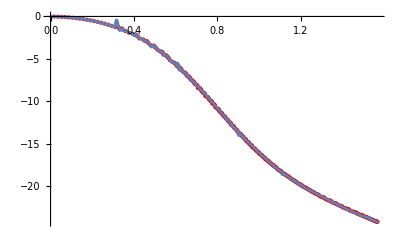

```mathematica
θaccs=χ*Accumulate[(Dτs*uτs-Drs*urs)[[1;;-2]]*fmtoIGeV*dαs];(*dimensionless*)
θacc=Interpolation[Transpose@{αs[[1;;-2]],θaccs}];
Show[
ListPlot[Transpose@{αs[[1;;-2]],θaccs},PlotStyle->{Directive[Red,PointSize[Medium]]}],
Plot[θacc[α],{α,0,Pi/2}]
]
```

It is useful to FIRST interpolate the input data and generate evenly spaced α values and SECOND use numerical integration via Accumulate.

```mathematica
(*Why does this not work with "=" instead of ":="*)
logspace[a_,b_,n_]:=10.0^Range[a,b,(b-a)/(n-1)];
linspace[a_,b_,n_]:=Range[a,b,(b-a)/(n-1)];

Nαs=1500
αs=linspace[0,Pi/2,Nαs];
dαs=(Pi/2)/Nαs;
urs=ur[αs]; (*dimensionless*)
uτs=uτ[αs]; (*dimensionless*)
rs=r[αs];(*in IGeV*)
Drs=Dr[αs];(*in IGeV*)
τs=τ[αs];(*in IGeV*)
Dτs=Dτ[αs];
```

1500

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {π/2998} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {π/1499} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

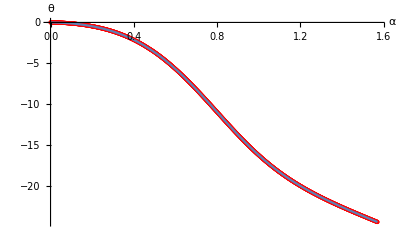

```mathematica
θaccs=χ*Accumulate[(Dτs*uτs-Drs*urs)*fmtoIGeV*dαs];(*dimensionless*)
θacc=Interpolation[Transpose@{αs,θaccs}];
Show[
ListPlot[Transpose@{αs,θaccs},PlotStyle->{Directive[Red,PointSize[Medium]]},AxesLabel->{α,θ}],
Plot[θacc[α],{α,0,Pi/2},AxesLabel->{α,θ}]
]
```

The result can now be used to define the sigma and pion fields on the freezeout surface.

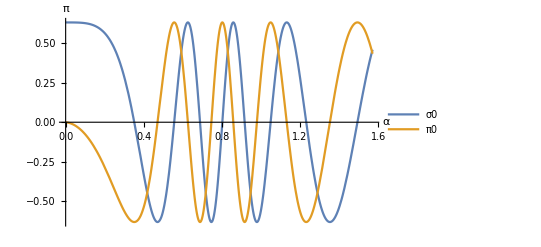

```mathematica
ϕ0[α_]=ρ*Exp[I*θacc[α]];(*in GeV*)
π0[α_]=Sqrt[2]*Im[ϕ0[α]];(*in GeV*)
σ0[α_]=Sqrt[2]*Re[ϕ0[α]];(*in GeV*)
Plot[{σ0[α],π0[α]},{α,0,Pi/2},
PlotLegends->{σ0,π0},
AxesLabel->{α,Pi}]
```

### What about these error messages due to nested calls to NIntegrate?

```mathematica
f[x_?NumericQ]:=NIntegrate[t,{t,0,x}](*1/2 x^2*)
k[x_?NumericQ]:=Re[f[x]]
h=NIntegrate[Evaluate[k[x]],{x,0,1}]
```

0.166667

```mathematica
f[x_?NumericQ]:=NIntegrate[t,{t,0,x}](*1/2 x^2*)
h=NIntegrate[Evaluate[f[x]],{x,0,1}]
```

0.166667

```mathematica
g[y_]:=NIntegrate[f[x],{x,0,y}]
g[1]
```

0.166667

## Compute the Fourier Spectrum of the Source

First, define a set of helper functions. These depend on the (transverse) momentum p_ and the coordinate α_ on the Freezeout surface. Eventually we wish to integrate over the Freezeout surface. The dependence on p_ can be substituted by explicit evaluation on a (nicely resolved) grid in momentum space. The dependence on α_ must remain symbolic, since we wish to numerically integrate over α_ using NIntegrate.

```mathematica
mπ=0.14;(*in GeV, mπ0=134.9768 MeV, mπ+-=139.57039 MeV *)
ω[p_]=Sqrt[p^2+mπ^2];(*in GeV (p in GeV) *)
J0rp[α_,p_]=BesselJ[0,r[α]*p*GeVtoIfm];(*dimensionless*)
J1rp[α_,p_]=BesselJ[1,r[α]*p*GeVtoIfm];(*dimensionless*)
Y0tw[α_,p_]=BesselY[0,τ[α]*ω[p]*GeVtoIfm];(*dimensionless*)
Y1tw[α_,p_]=BesselY[1,τ[α]*ω[p]*GeVtoIfm];(*dimensionless*)
J0tw[α_,p_]=BesselJ[0,τ[α]*ω[p]*GeVtoIfm];(*dimensionless*)
J1tw[α_,p_]=BesselJ[1,τ[α]*ω[p]*GeVtoIfm];(*dimensionless*)

H1[α_,p_]=J0rp[α,p]*(-Y0tw[α,p]+I*J0tw[α,p]);(*dimensionless*)
H2[α_,p_]=Dτ[α]*fmtoIGeV*p*J1rp[α,p]*(-Y0tw[α,p]+I*J0tw[α,p])+(*dimensionless*)
Dr[α]*fmtoIGeV*J0rp[α,p]*ω[p]*(-Y1tw[α,p]+I*J1tw[α,p]);(*dimensionless*)
```

NOTATION: an object named "fps" with f some quantity represents a function f[p_,...] with the p_-dependence evaluated explicitly on the momentum grid given by "ps".

```mathematica
ps=linspace[0,2,50];
Print[Min[ps]," to ",Max[ps], " GeV"]
```

0 to 2 GeV

```mathematica
(*σ0=σfreeze*Cos[θ0]-πfreeze*Sin[θ0]
π0=πfreeze*Cos[θ0]+σfreeze*Sin[θ0]*)
H1ps[α_]=H1[α,ps];
H2ps[α_]=H2[α,ps];
```

The most ressource heavy computation happens here, due to the use of NIntegrate. The routine (probably) uses more and more subdivisions for the large-p_ components in H(1/2)ps.

WHY USE NINTEGRATE AND INTERPOLATED FUNCTIONS? Discrete Fourier Transform, say  on  an  Interval [0, L], discretized  with  N  points, shows  and  alias  effect  and  is  valid  only  up  to  the  Nyquist  frequency  (~ momentum)  (2?)  Nπ/L  and  the  spectrum  will  then  continue  periodically  (just  as  the  real  space  function  will, if  calculated  from  discretized  momentum  grid . There  will  thus  be  no  convergence  to  0  for  large  momenta . It  is  not  immediately  clear  to  me  how  this  effect  is  altered  when  using  Bessel  functions  and  the  integral  measure  in  polar  coordinates, but  qualitatively  this  should  prevent  convergence  to  0  of  the  spectrum  for  large  p, which  would  be  necessary  for  a  physical  spectrum . 
    
    One  could  simply  apply  a  finer  discretization  in  real  space  (= finer  mesh  of  αs), but  I  expect  the  effect  to  be  worse  for  larger  momenta . The  routine  NIntegrate  automatically  chooses  and  refines  the  grid  of  αs  in  real  space, until  the  integral  has  converged  sufficiently  well . For  low  p_  it  is  expected  that  the  grid  specified  by  the  raw  data  is  enough . For  large  p_  a  finer  grid  should  be  chosen . We  should  thus  provide  (interpolated)  functions  of  α_  such  that  this  refinement  through  the  integration  routine is dynamically possible .

```mathematica
(*The C's all have dimension IGeV*)
{time1,C1σps}=Timing[2*Pi^2*NIntegrate[τ[α]*r[α]*fmtoIGeV^2*(-1)*π0[α]*χ*(-Dr[α]*uτ[α]+Dτ[α]*ur[α])*H1ps[α],{α,0,Pi/2}]];
Print[time1, " seconds"]
{time2,C1πps}=Timing[2*Pi^2*NIntegrate[τ[α]*r[α]*fmtoIGeV^2*σ0[α]*χ*(-Dr[α]*uτ[α]+Dτ[α]*ur[α])*H1ps[α],{α,0,Pi/2}]];
Print[time2, " seconds"]
{time3,C2σps}=Timing[2*Pi^2*NIntegrate[τ[α]*r[α]*fmtoIGeV^2*σ0[α]*H2ps[α],{α,0,Pi/2}]];
Print[time3, " seconds"]
{time4,C2πps}=Timing[2*Pi^2*NIntegrate[τ[α]*r[α]*fmtoIGeV^2*π0[α]*H2ps[α],{α,0,Pi/2}]];
Print[time4, " seconds"]
(*
C1σ=2*Pi^2*Total[dalpha*taus*rs*fmtoIGeV^2*((-1)*π0*χ*(-drs*utau+dtaus*ur)*H1ps)];(*I guess u_tau=-u^tau*)
C1π=2*Pi^2*Total[dalpha*taus*rs*fmtoIGeV^2*(σ0*χ*(-drs*utau+dtaus*ur)*H1ps)];
C2σ=2*Pi^2*Total[dalpha*taus*rs*fmtoIGeV^2*σ0*H2ps];
C2π=2*Pi^2*Total[dalpha*taus*rs*fmtoIGeV^2*π0*H2ps];
*)

Jps[θ0_]=(C1σps+C2σps)*Sin[θ0]+(C1πps+C2πps)*Cos[θ0];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {1.09831}. NIntegrate obtained 91.6736+54.6516 ⅈ and 0.00224251 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {1.09831}. NIntegrate obtained 59.2937+77.8191 ⅈ and 0.000774676 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {1.09831}. NIntegrate obtained -28.3103+70.3083 ⅈ and 0.000797146 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

20.6477 seconds

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {1.11671}. NIntegrate obtained 12.9414+21.0819 ⅈ and 0.00293993 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {1.11671}. NIntegrate obtained 7.85538+30.8246 ⅈ and 0.00103261 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {1.11671}. NIntegrate obtained -39.0399+39.7518 ⅈ and 0.00101265 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

17.9868 seconds

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.478578}. NIntegrate obtained -16.0861-7.84662 ⅈ and 0.0221431 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.478578}. NIntegrate obtained -67.8543+28.7908 ⅈ and 0.0137173 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.478578}. NIntegrate obtained -185.511-92.5917 ⅈ and 0.0108076 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

25.8698 seconds

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.681063}. NIntegrate obtained 252.236-192.52 ⅈ and 0.0105093 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.681063}. NIntegrate obtained 245.062-122.305 ⅈ and 0.00502202 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.681063}. NIntegrate obtained 156.283+34.3524 ⅈ and 0.00476859 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

37.8608 seconds

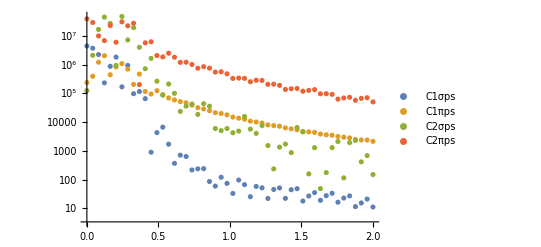

```mathematica
ListLogPlot[
{Transpose@{ps,Abs[C1σps]^2},
Transpose@{ps,Abs[C1πps]^2},
Transpose@{ps,Abs[C2σps]^2},
Transpose@{ps,Abs[C2πps]^2}},
PlotLegends->{"C1σps","C1πps","C2σps","C2πps"}
]
```

```mathematica
Manipulate[
ListLogPlot[Transpose@{ps,Abs[Jps[θ0]]^2},AxesLabel->{"p [GeV]","|π(p)|^2"}]
,{θ0,0,2*Pi}]
```

Transpose::nmtx: The first two levels of {{0,2/49,4/49,6/49,8/49,10/49,12/49,2/7,16/49,18/49,«40»},Abs[Jps[0.]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0,0.04081632653061224,0.08163265306122449,0.1224489795918367,0.163265306122449,0.2040816326530612,0.2448979591836735,0.2857142857142857,0.326530612244898,0.3673469387755102,«40»},Abs[Jps[0.]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0.,0.0408163,0.0816327,0.122449,0.163265,0.204082,0.244898,0.285714,0.326531,0.367347,«40»},Abs[Jps[0.]]^2} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLogPlot::lpn: Transpose[{{0,0.04081632653061224,0.08163265306122449,0.1224489795918367,0.163265306122449,0.2040816326530612,0.2448979591836735,0.2857142857142857,0.326530612244898,0.3673469387755102,«40»},Abs[Jps[0.]]^2}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {{0,2/49,4/49,6/49,8/49,10/49,12/49,2/7,16/49,18/49,«40»},Abs[Jps[0.]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0,0.04081632653061224,0.08163265306122449,0.1224489795918367,0.163265306122449,0.2040816326530612,0.2448979591836735,0.2857142857142857,0.326530612244898,0.3673469387755102,«40»},Abs[Jps[0.]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0.,0.0408163,0.0816327,0.122449,0.163265,0.204082,0.244898,0.285714,0.326531,0.367347,«40»},Abs[Jps[0.]]^2} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLogPlot::lpn: Transpose[{{0,0.04081632653061224,0.08163265306122449,0.1224489795918367,0.163265306122449,0.2040816326530612,0.2448979591836735,0.2857142857142857,0.326530612244898,0.3673469387755102,«40»},Abs[Jps[0.]]^2}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {{0,2/49,4/49,6/49,8/49,10/49,12/49,2/7,16/49,18/49,«40»},Abs[Jps[0.]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0,0.04081632653061224,0.08163265306122449,0.1224489795918367,0.163265306122449,0.2040816326530612,0.2448979591836735,0.2857142857142857,0.326530612244898,0.3673469387755102,«40»},Abs[Jps[0.]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0.,0.0408163,0.0816327,0.122449,0.163265,0.204082,0.244898,0.285714,0.326531,0.367347,«40»},Abs[Jps[0.]]^2} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLogPlot::lpn: Transpose[{{0,0.04081632653061224,0.08163265306122449,0.1224489795918367,0.163265306122449,0.2040816326530612,0.2448979591836735,0.2857142857142857,0.326530612244898,0.3673469387755102,«40»},Abs[Jps[0.]]^2}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {{0,2/49,4/49,6/49,8/49,10/49,12/49,2/7,16/49,18/49,«40»},Abs[Jps[0.]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0,0.04081632653061224,0.08163265306122449,0.1224489795918367,0.163265306122449,0.2040816326530612,0.2448979591836735,0.2857142857142857,0.326530612244898,0.3673469387755102,«40»},Abs[Jps[0.]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0.,0.0408163,0.0816327,0.122449,0.163265,0.204082,0.244898,0.285714,0.326531,0.367347,«40»},Abs[Jps[0.]]^2} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLogPlot::lpn: Transpose[{{0,0.04081632653061224,0.08163265306122449,0.1224489795918367,0.163265306122449,0.2040816326530612,0.2448979591836735,0.2857142857142857,0.326530612244898,0.3673469387755102,«40»},Abs[Jps[0.]]^2}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {{0,2/49,4/49,6/49,8/49,10/49,12/49,2/7,16/49,18/49,«40»},Abs[Jps[0.]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0,0.04081632653061224,0.08163265306122449,0.1224489795918367,0.163265306122449,0.2040816326530612,0.2448979591836735,0.2857142857142857,0.326530612244898,0.3673469387755102,«40»},(«1»)^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0.,0.0408163,0.0816327,0.122449,0.163265,0.204082,0.244898,0.285714,0.326531,0.367347,«40»},Abs[Jps[0.]]^2} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLogPlot::lpn: Transpose[{{0,0.04081632653061224,0.08163265306122449,0.1224489795918367,0.163265306122449,«44»,0.2448979591836735,0.2857142857142857,0.326530612244898,0.3673469387755102,«40»},Abs[Jps[0.]]^2}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {{0,10/49,20/49,30/49,40/49,50/49,60/49,10/7,80/49,90/49,«40»},Abs[Jps[0.]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0,0.2040816326530612,0.4081632653061224,0.6122448979591837,0.8163265306122449,1.020408163265306,1.224489795918367,1.428571428571429,1.63265306122449,1.836734693877551,«40»},(«1»)^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0.,0.204082,0.408163,0.612245,0.816327,1.02041,1.22449,1.42857,1.63265,1.83673,«40»},Abs[Jps[0.]]^2} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLogPlot::lpn: Transpose[{{0,0.2040816326530612,0.4081632653061224,0.6122448979591837,0.8163265306122449,«44»,1.224489795918367,1.428571428571429,1.63265306122449,1.836734693877551,«40»},Abs[Jps[0.]]^2}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {{0,2/49,4/49,6/49,8/49,10/49,12/49,2/7,16/49,18/49,«40»},Abs[Jps[0.]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0,0.04081632653061224,0.08163265306122449,0.1224489795918367,0.163265306122449,0.2040816326530612,0.2448979591836735,0.2857142857142857,0.326530612244898,0.3673469387755102,«40»},(«1»)^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0.,0.0408163,0.0816327,0.122449,0.163265,0.204082,0.244898,0.285714,0.326531,0.367347,«40»},Abs[Jps[0.]]^2} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLogPlot::lpn: Transpose[{{0,0.04081632653061224,0.08163265306122449,0.1224489795918367,0.163265306122449,«44»,0.2448979591836735,0.2857142857142857,0.326530612244898,0.3673469387755102,«40»},Abs[Jps[0.]]^2}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {{0,2/49,4/49,6/49,8/49,10/49,12/49,2/7,16/49,18/49,«40»},Abs[Jps[0.]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0,0.04081632653061224,0.08163265306122449,0.1224489795918367,0.163265306122449,0.2040816326530612,0.2448979591836735,0.2857142857142857,0.326530612244898,0.3673469387755102,«40»},(«1»)^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0.,0.0408163,0.0816327,0.122449,0.163265,0.204082,0.244898,0.285714,0.326531,0.367347,«40»},Abs[Jps[0.]]^2} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLogPlot::lpn: Transpose[{{0,0.04081632653061224,0.08163265306122449,0.1224489795918367,0.163265306122449,«44»,0.2448979591836735,0.2857142857142857,0.326530612244898,0.3673469387755102,«40»},Abs[Jps[0.]]^2}] is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {{0,2/49,4/49,6/49,8/49,10/49,12/49,2/7,16/49,18/49,«40»},Abs[Jps[0.]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0,0.04081632653061224,0.08163265306122449,0.1224489795918367,0.163265306122449,0.2040816326530612,0.2448979591836735,0.2857142857142857,0.326530612244898,0.3673469387755102,«40»},Abs[Jps[0.]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0.,0.0408163,0.0816327,0.122449,0.163265,0.204082,0.244898,0.285714,0.326531,0.367347,«40»},Abs[Jps[0.]]^2} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLogPlot::lpn: Transpose[{{0.,0.0408163,0.0816327,0.122449,0.163265,0.204082,0.244898,0.285714,0.326531,0.367347,«40»},Abs[Jps[0.]]^2}] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogPlot::lpn will be suppressed during this calculation.

## All of the Above In a Single Function

```mathematica
(*
π0=...;
Dπ0=σ0[α]*χ*(-Dr[α]*uτ[α]+Dτ[α]*ur[α]);
*)
ComputeSourceSpectr[ps_,f_,Df_]:=Module[{H1ps,H2ps,spectrps},
(*
f is supposed to be the π-field, Df it's perpendiculat derivative, 
Df = r'*D[f,τ]+τ'*D[f,r]

The name π is protected!!!
*)
H1ps[α_]=H1[α,ps];
H2ps[α_]=H2[α,ps];

spectrps=2*Pi^2*NIntegrate[τ[α]*r[α]*fmtoIGeV^2*(Df[α]*H1ps[α]+f[α]*H2ps[α]),{α,0,Pi/2}];
spectrps
]
```

```mathematica
ps=linspace[0,10,100];
Jπspec=ComputeSourceSpectr[ps,π0[#]&,σ0[#]*χ*(-Dr[#]*uτ[#]+Dτ[#]*ur[#])&];
Jσspec=ComputeSourceSpectr[ps,σ0[#]&,-1*π0[#]*χ*(-Dr[#]*uτ[#]+Dτ[#]*ur[#])&];
Jπspecfinal[θ0_]=Jσspec*Sin[θ0]+Jπspec*Cos[θ0];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.681063}. NIntegrate obtained 266.12-171.942 ⅈ and 0.010821 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.681063}. NIntegrate obtained 38.381+72.876 ⅈ and 0.00506432 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.681063}. NIntegrate obtained -113.326+47.0983 ⅈ and 0.00380605 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.478578}. NIntegrate obtained 74.4993+45.9966 ⅈ and 0.0216289 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.478578}. NIntegrate obtained -166.053-215.267 ⅈ and 0.0108559 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in α near {α} = {0.478578}. NIntegrate obtained -43.2098-44.0005 ⅈ and 0.0103489 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

This does exactly the same as before:

```mathematica
Manipulate[
ListLogPlot[
Transpose@{ps,Abs[Jπspecfinal[θ0]]^2},
AxesLabel->{"p [GeV]","|π(p)|^2"},
PlotRange->{{0,1},{10^2,5*10^7}}],
{θ0,0,2*Pi}]
```

```mathematica
Manipulate[
ListLogPlot[
{Transpose@{ps,Abs[Jπspecfinal[θ0]]^2},Transpose@{ps,Abs[Jps[θ0]]^2}},
PlotMarkers->{{Graphics[{Red,Circle[]}],0.04},{Graphics[{Blue,Rectangle[]}],0.02}}
,AxesLabel->{"p [GeV]","|π(p)|^2"}]
,{θ0,0,2*Pi}]
```

Transpose::nmtx: The first two levels of {{0,2/49,4/49,6/49,8/49,10/49,12/49,2/7,16/49,18/49,«40»},Abs[Jπspecfinal[0.]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0,2/49,4/49,6/49,8/49,10/49,12/49,2/7,16/49,18/49,«40»},Abs[Jps[0.]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0,0.04081632653061224,0.08163265306122449,0.1224489795918367,0.163265306122449,0.2040816326530612,0.2448979591836735,0.2857142857142857,0.326530612244898,0.3673469387755102,«40»},Abs[Jπspecfinal[0.]]^2} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{0,2/49,4/49,6/49,8/49,10/49,12/49,2/7,16/49,18/49,«40»},Abs[Jps[0.]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0,0.04081632653061224,0.08163265306122449,0.1224489795918367,0.163265306122449,0.2040816326530612,0.2448979591836735,0.2857142857142857,0.326530612244898,0.3673469387755102,«40»},Abs[Jps[0.]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0.,0.0408163,0.0816327,0.122449,0.163265,0.204082,0.244898,0.285714,0.326531,0.367347,«40»},Abs[Jps[0.]]^2} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLogPlot::lpn: {{{0,17.4752},{0.04081632653061224,17.1543},{0.08163265306122449,15.8298},{0.1224489795918367,14.1596},{0.163265306122449,16.7048},{«1»},{«44»,«19»},{0.2857142857142857,16.8703},{0.326530612244898,17.1195},{0.3673469387755102,13.3039},«40»},{}} is not a list of numbers or pairs of numbers.

Transpose::nmtx: The first two levels of {{0,2/49,4/49,6/49,8/49,10/49,12/49,2/7,16/49,18/49,«40»},Abs[Jπspecfinal[0.]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0,2/49,4/49,6/49,8/49,10/49,12/49,2/7,16/49,18/49,«40»},Abs[Jps[0.]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0,0.04081632653061224,0.08163265306122449,0.1224489795918367,0.163265306122449,0.2040816326530612,0.2448979591836735,0.2857142857142857,0.326530612244898,0.3673469387755102,«40»},Abs[Jπspecfinal[0.]]^2} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{0,2/49,4/49,6/49,8/49,10/49,12/49,2/7,16/49,18/49,«40»},Abs[0.+1. ComputeSourceSpectr[{0,2/49,4/49,6/49,8/49,10/49,12/49,2/7,16/49,18/49,«40»},π0[«1»]&,Times[«3»]&]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0,2/49,4/49,6/49,8/49,10/49,12/49,2/7,16/49,18/49,«40»},Abs[Jps[0.]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0,0.04081632653061224,0.08163265306122449,0.1224489795918367,0.163265306122449,0.2040816326530612,0.2448979591836735,0.2857142857142857,0.326530612244898,0.3673469387755102,«40»},Abs[0.+1. ComputeSourceSpectr[«1»]]^2} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{0,2/49,4/49,6/49,8/49,10/49,12/49,2/7,16/49,18/49,«40»},Abs[Jπspecfinal[0.]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0,2/49,4/49,6/49,8/49,10/49,12/49,2/7,16/49,18/49,«40»},Abs[Jps[0.]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0,0.04081632653061224,0.08163265306122449,0.1224489795918367,0.163265306122449,0.2040816326530612,0.2448979591836735,0.2857142857142857,0.326530612244898,0.3673469387755102,«40»},Abs[Jπspecfinal[0.]]^2} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{0,2/49,4/49,6/49,8/49,10/49,12/49,2/7,16/49,18/49,«40»},Abs[Jps[0.]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0,0.04081632653061224,0.08163265306122449,0.1224489795918367,0.163265306122449,0.2040816326530612,0.2448979591836735,0.2857142857142857,0.326530612244898,0.3673469387755102,«40»},Abs[Jps[0.]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0.,0.0408163,0.0816327,0.122449,0.163265,0.204082,0.244898,0.285714,0.326531,0.367347,«40»},Abs[Jps[0.]]^2} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLogPlot::lpn: {{{0.,17.482},{0.0408163,17.1581},{0.0816327,15.826},{0.122449,14.1487},{0.163265,16.7174},{0.204082,15.3917},{0.244898,17.0537},{0.285714,16.8712},{0.326531,17.1207},{0.367347,13.345},«40»},{}} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogPlot::lpn will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{0,2/49,4/49,6/49,8/49,10/49,12/49,2/7,16/49,18/49,«40»},Abs[Jps[0.]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0,0.04081632653061224,0.08163265306122449,0.1224489795918367,0.163265306122449,0.2040816326530612,0.2448979591836735,0.2857142857142857,0.326530612244898,0.3673469387755102,«40»},Abs[Jps[0.]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0.,0.0408163,0.0816327,0.122449,0.163265,0.204082,0.244898,0.285714,0.326531,0.367347,«40»},Abs[Jps[0.]]^2} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLogPlot::lpn: {{{0.,17.482},{0.0408163,17.1581},{0.0816327,15.826},{0.122449,14.1487},{0.163265,16.7174},{0.204082,15.3917},{0.244898,17.0537},{0.285714,16.8712},{0.326531,17.1207},{0.367347,13.345},«40»},{}} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogPlot::lpn will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{0,1/99,2/99,1/33,4/99,5/99,2/33,7/99,8/99,1/11,«90»},Abs[Jps[0.]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0,0.0101010101010101,0.0202020202020202,0.0303030303030303,0.0404040404040404,0.05050505050505051,0.06060606060606061,0.07070707070707071,0.08080808080808081,0.09090909090909091,«90»},Abs[Jps[0.]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0.,0.010101,0.020202,0.030303,0.040404,0.0505051,0.0606061,0.0707071,0.0808081,0.0909091,«90»},Abs[Jps[0.]]^2} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLogPlot::lpn: {{{0.,17.482},{0.010101,17.4655},{0.020202,17.4132},{0.030303,17.3171},{0.040404,17.1656},{0.0505051,16.947},{0.0606061,16.6535},{0.0707071,16.2876},{0.0808081,15.8629},{0.0909091,15.3818},«90»},{}} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogPlot::lpn will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{0,10/99,20/99,10/33,40/99,50/99,20/33,70/99,80/99,10/11,«90»},Abs[Jps[0.]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0,0.101010101010101,0.202020202020202,0.303030303030303,0.404040404040404,0.5050505050505051,0.6060606060606061,0.7070707070707071,0.8080808080808081,0.9090909090909091,«90»},Abs[Jps[0.]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0.,0.10101,0.20202,0.30303,0.40404,0.505051,0.606061,0.707071,0.808081,0.909091,«90»},Abs[Jps[0.]]^2} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

ListLogPlot::lpn: {{{0.,17.482},{0.10101,14.7875},{0.20202,15.5851},{0.30303,11.6083},{0.40404,16.0412},{0.505051,15.1675},{0.606061,14.7359},{0.707071,14.4493},{0.808081,14.0169},{0.909091,13.5221},«90»},{}} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogPlot::lpn will be suppressed during this calculation.

## Come up with different initial conditions?

```mathematica
constone[x_]:=1;
constzero[x_]:=0;
ps=linspace[0,10,50];
Jπspec=ComputeSourceSpectr[ps,constone[#]&,constzero[#]&];
```

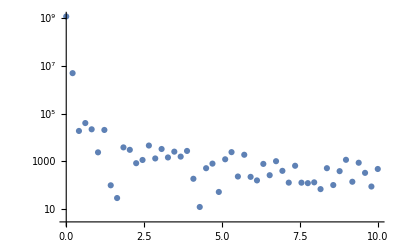

```mathematica
ListLogPlot[Transpose@{ps,Abs[Jπspec]^2}]
```

```mathematica
Abs@Jπspec^2
```

{1.19476×10^9,4.97032×10^6,18598.3,39892.7,21801.,2350.7,20478.9,97.0901,28.3285,3795.23,2999.95,823.326,1122.57,4539.83,1301.98,3247.32,1434.33,2514.41,1556.64,2691.96,182.523,11.9267,507.303,790.218,51.0108,1200.97,2398.25,227.218,1861.2,219.471,155.816,768.617,257.697,998.7,392.785,125.687,642.148,125.071,119.542,129.07,67.1037,507.75,99.4942,381.432,1143.22,136.777,860.426,323.45,86.229,470.331}

## Compare to Alice Data

```mathematica
Alicedatatxt=Import[StringJoin[NotebookDirectory[],"data/HEPData-ins1222333-v1-Table_1.csv"],"Text"];
(*Alicedata=ImportString[StringReplace[StringReplace[Alicedatatxt,RegularExpression["\n+"]->"\n"],StartOfLine~~"#"~~Shortest[___]~~EndOfLine~~"\n"->""],"CSV"];*)
Alicedata=ImportString[StringReplace[Alicedatatxt,StartOfLine~~"#"~~Shortest[___]~~EndOfLine~~"\n"->""],"CSV","IgnoreEmptyLines"->True];
MatrixForm[Alicedata];
titles=Alicedata[[1]];
enumeratedtitles=Transpose[{Range[Length[titles]],titles}]
πplus=Alicedata[[2;;42]];
πminus=Alicedata[[44;;]];
aliceps=(Transpose@πplus)[[1]];
aliceyieldplus=(Transpose@πplus)[[4]];
aliceyieldminus=(Transpose@πminus)[[4]];
```

{{1,PT [GEV]},{2,PT [GEV] LOW},{3,PT [GEV] HIGH},{4,(1/Nev)*(1/(2*PI*PT))*D2(N)/DPT/DYRAP [GEV**-2]},{5,stat +},{6,stat -},{7,sys +},{8,sys -},{9,sys,normalization uncertainty +},{10,sys,normalization uncertainty -}}

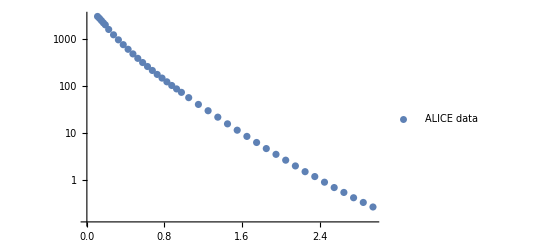

```mathematica
ListALICE=Transpose@{aliceps,aliceyieldplus+aliceyieldminus};
ListLogPlot[
ListALICE,
PlotLegends->{"ALICE data"}
]
```

```mathematica
Manipulate[
ListLogPlot[
{ListALICE,Transpose@{ps,1/(2*Pi)^3*Abs[Jps[θ0]]^2}},
PlotLegends->{"ALICE","myspectr"}
]
,{θ0,0,2*Pi}
]
```

Transpose::nmtx: The first two levels of {{0,2/49,4/49,6/49,8/49,10/49,12/49,2/7,16/49,18/49,«40»},Abs[Jps[1.64619]]^2/(8 π^3)} cannot be transposed.

Transpose::nmtx: The first two levels of {{0,0.04081632653061224,0.08163265306122449,0.1224489795918367,0.163265306122449,0.2040816326530612,0.2448979591836735,0.2857142857142857,0.326530612244898,0.3673469387755102,«40»},0.00403144180414994 Abs[Jps[«19»]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0.,0.0408163,0.0816327,0.122449,0.163265,0.204082,0.244898,0.285714,0.326531,0.367347,«40»},0.00403144 Abs[Jps[1.64619]]^2} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{0,2},Abs[Jps[1.64619]]^2/(8 π^3)} cannot be transposed.

Transpose::nmtx: The first two levels of {{0,2.},0.00403144180414994 Abs[Jps[1.64619]]^2} cannot be transposed.

Transpose::nmtx: The first two levels of {{0.,2.},0.00403144 Abs[Jps[1.64619]]^2} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {{0,10/49,20/49,30/49,40/49,50/49,60/49,10/7,80/49,90/49,«40»},Abs[Jps[1.64619]]^2/(8 π^3)} cannot be transposed.

Transpose::nmtx: The first two levels of {{0,0.2040816326530612,0.4081632653061224,0.6122448979591837,0.8163265306122449,1.020408163265306,1.224489795918367,1.428571428571429,1.63265306122449,1.836734693877551,«40»},«59» «1»} cannot be transposed.

Transpose::nmtx: The first two levels of {{0.,0.204082,0.408163,0.612245,0.816327,1.02041,1.22449,1.42857,1.63265,1.83673,«40»},0.00403144 Abs[Jps[1.64619]]^2} cannot be transposed.

General::stop: Further output of Transpose::nmtx will be suppressed during this calculation.